See 
http://en.wikipedia.org/wiki/Joseph_Kittinger
http://en.wikipedia.org/wiki/Project_Excelsior
http://hypertextbook.com/facts/JianHuang.shtml

Velocity of a falling object is determined by 

v(t) = (m*g/k)(1-e^(-kt/m))

where g is the acceleration due to gravity, and k is a constant, m is the mass of the object. This is a very rough approximation. 

NOOOO See:

http://galileo.phys.virginia.edu/classes/581/DragCalculus.html

```mathematica
m=140;
g=10.;
Solve[m*g/K==274,K]
Solve[m*g ==b*274^2,b]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{K→5.10949}}

{{b→0.0186478}}

274.51 (1-ⅇ^(-0.0364286 t))

274 Tanh[0.0364029 t]

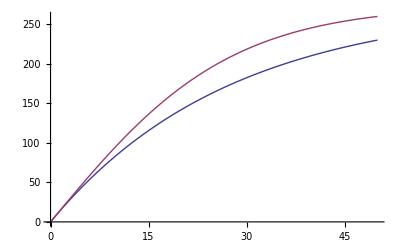

{t→123.057}

{t→115.13}

```mathematica
k=5.1;
v[t_]=m*g/k(1-E^(-k*t/m))
w[t_]=274*Tanh[274*.0186*t/140]
(*v[t_]=m*g/k(1-.7^(t)) *)
Plot[{v[t],w[t]},{t,0,50}]

p[t_]=Integrate[v[x],{x,0,t}];
q[t_]=Integrate[w[x],{x,0,t}];
FindRoot[p[t]-31330+5000,{t,100}]
FindRoot[q[t]-31330+5000,{t,400}]
```

```mathematica
FindRoot[ConditionalExpression[7777.777777777779 Log[Cosh[0.03522857142857142 t]]==26330,Cosh[0.035228571428571421597641943890266702510416507720947265625`20.954589770191003 t]≥0],t]
```

FindRoot::fdss: Search specification t should be a list with 1 to 5 elements.

FindRoot[ConditionalExpression[7777.78 Log[Cosh[0.0352286 t]]==26330,Cosh[0.035228571428571421598 t]≥0],t]

After 4000 meters, a terminal velocity was attained....

```mathematica
v[17.39]
```

273.568

```mathematica
v[0]
```

0.

```mathematica
f[x_]=((x^3+4)^2-x^6)/x^3
```

(-x^6+(4+x^3)^2)/x^3

```mathematica
f[100000.]
```

8.02204